```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/katelinschutz/Desktop/Dropbox/AxionSIMPmediator/katelin's code/python scripts

```mathematica
Directory[]
```

/Users/katelinschutz

```mathematica
neq[T_, m_, d_] = d /(2 Pi^2) m^2 T BesselK[2, m/T];
ρeq[T_, m_, d_, μ_] = d /(2 Pi^2) m^2 T^2(3  BesselK[2, m/T]+m/T BesselK[1, m/T])Exp[μ/T];
peq[T_, m_, d_, μ_] = d /(2 Pi^2) m^2 T^2 BesselK[2, m/T]Exp[μ/T];
```

```mathematica
derivs={0,0,0,0};
```

```mathematica
derivs[[2]] = Module[{Tpi =(vpi+1)/a, μpi = (vpi+1)/a* Log[upi+1],Ta =(va+1)/a,μa = (va+1)/a* Log[ua+1]} , ((vpi+1)/a + 1/D[ρeq[f, mpi, dofpi, μpi], f] (- 3(ρeq[Tpi, mpi, dofpi, μpi]+ peq[Tpi, mpi, dofpi, μpi])+ a^2/H0 (constpiapiaE *neq[Tpi, mpi, dofpi]neq[Ta, ma, dofa]*(upi+1)(ua+1)-constpipiaaE neq[Tpi, mpi, dofpi]^2(upi+1)^2 + constaapipiE neq[Ta, ma, dofa]^2(ua+1)^2)))/.f-> Tpi];
```

```mathematica
derivs[[4]] = Module[{Tpi =(vpi+1)/a, μpi = (vpi+1)/a* Log[upi+1],Ta =(va+1)/a,μa = (va+1)/a* Log[ua+1]} , ((va+1)/a + 1/D[ρeq[f, ma, dofa, μa], f] (- 3(ρeq[Ta, ma, dofa, μa]+ peq[Ta, ma, dofa, μa])+ a^2/H0 (-constpiapiaE *neq[Tpi, mpi, dofpi]neq[Ta, ma, dofa]*(upi+1)(ua+1)+constpipiaaE neq[Tpi, mpi, dofpi]^2(upi+1)^2 - constaapipiE neq[Ta, ma, dofa]^2(ua+1)^2 + constggaE *Ta/a*BesselK[1, ma/Ta]- constaggE *Ta^2*BesselK[1, ma/Ta] (ua+1))  ))/.f-> Ta];
```

```mathematica
derivs[[1]] = Module[{Tpi =(vpi+1)/a, μpi = (vpi+1)/a* Log[upi+1],Ta =(va+1)/a,μa = (va+1)/a* Log[ua+1]} , (-(upi+1)/neq[Tpi, mpi, dofpi] D[neq[f, mpi, dofpi], f] * (derivs[[2]]- Tpi)/a - 3(upi+1)/a + a/(H0 neq[Tpi, mpi, dofpi])(-constpipiaa neq[Tpi, mpi, dofpi]^2 (upi+1)^2 + constaapipi neq[Ta, ma, dofa]^2(ua+1)^2 - constWZW *Tpi^2 *neq[Tpi, mpi, dofpi]^3upi(upi+1)))/.f->Tpi];
```

```mathematica
derivs[[3]] = Module[{Tpi =(vpi+1)/a, μpi = (vpi+1)/a* Log[upi+1],Ta =(va+1)/a,μa = (va+1)/a* Log[ua+1]} , (-(ua+1)/neq[Ta, ma, dofa] D[neq[f, ma, dofa], f] * (derivs[[4]]- Ta)/a - 3(ua+1)/a + a/(H0 neq[Ta, ma, dofa])(+constpipiaa neq[Tpi, mpi, dofpi]^2 (upi+1)^2 - constaapipi neq[Ta, ma, dofa]^2(ua+1)^2 +Ta BesselK[1, ma/Ta] constgga    - Ta*BesselK[1, ma/Ta]constagg (ua+1)))/.f->Ta];
```

```mathematica
derivs/.constagg->0/.constaggE->0/.constgga->0/.constggaE->0/.constgga->0/.constaapipi->0/.constaapipiE->0/.constpiapiaE->-2.2270042552813636*10^-14/.constpiapiaE->0/.constpipiaa->0/.constpipiaaE->0/.dofa->1/.dofpi->5/.mpi->1/.ma->0.1/.H0->2.*10^-19/.a->10/.upi->10^-2/.vpi->10.^-3/.ua->10.^-4/.va->10.^-5/.constWZW->0.078914969714913075*10^-10
```

{78.3641,-6.5865,-1.46772,0.44642}

```mathematica
vars = {upi, vpi, ua, va};
```

```mathematica
Table[D[derivs[[i]], vars[[j]]], {i, 4}, {j, 4}]/.constagg->0/.constaggE->0/.constgga->0/.constggaE->0/.constgga->0/.constaapipi->0/.constaapipiE->0/.constpiapiaE->-2.2270042552813636*10^-14/.constpiapiaE->0/.constpipiaa->0/.constpipiaaE->0/.dofa->1/.dofpi->5/.mpi->1/.ma->0.1/.H0->2.*10^-19/.a->10/.upi->10^-2/.vpi->10.^-3/.ua->10.^-4/.va->10.^-5/.constWZW->0.078914969714913075*10^-10
```

{{84.1853,-14.0773,78.3344,264.045},{-0.560742,-11.0185,-6.65832,-22.4434},{-1.46622,-17.25,-1.74645,1.33181},{0.434986,5.11756,0.0827348,0.114927}}

```mathematica
Export["jacobian00.txt",FortranForm[D[derivs[[1]], vars[[1]]]]]
Export["jacobian01.txt",FortranForm[D[derivs[[1]], vars[[2]]]]]
Export["jacobian02.txt",FortranForm[D[derivs[[1]], vars[[3]]]]]
Export["jacobian03.txt",FortranForm[D[derivs[[1]], vars[[4]]]]]
Export["jacobian10.txt",FortranForm[D[derivs[[2]], vars[[1]]]]]
Export["jacobian11.txt",FortranForm[D[derivs[[2]], vars[[2]]]]]
Export["jacobian12.txt",FortranForm[D[derivs[[2]], vars[[3]]]]]
Export["jacobian13.txt",FortranForm[D[derivs[[2]], vars[[4]]]]]
Export["jacobian20.txt",FortranForm[D[derivs[[3]], vars[[1]]]]]
Export["jacobian21.txt",FortranForm[D[derivs[[3]], vars[[2]]]]]
Export["jacobian22.txt",FortranForm[D[derivs[[3]], vars[[3]]]]]
Export["jacobian23.txt",FortranForm[D[derivs[[3]], vars[[4]]]]]
Export["jacobian30.txt",FortranForm[D[derivs[[4]], vars[[1]]]]]
Export["jacobian31.txt",FortranForm[D[derivs[[4]], vars[[2]]]]]
Export["jacobian32.txt",FortranForm[D[derivs[[4]], vars[[3]]]]]
Export["jacobian33.txt",FortranForm[D[derivs[[4]], vars[[4]]]]]
```

jacobian00.txt

jacobian01.txt

jacobian02.txt

jacobian03.txt

jacobian10.txt

jacobian11.txt

jacobian12.txt

jacobian13.txt

jacobian20.txt

jacobian21.txt

jacobian22.txt

jacobian23.txt

jacobian30.txt

jacobian31.txt

jacobian32.txt

jacobian33.txt

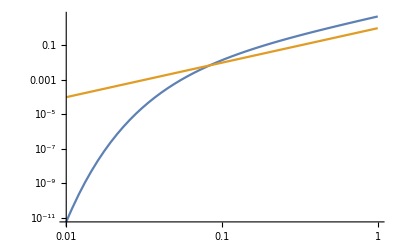

```mathematica
LogLogPlot[ {T BesselK[1,0.2/T], T^2}, {T, 10^-2, 1}]
```